### Start choosing the example:

```mathematica
t=23;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]/.{I1->312/100, U1->2,S1->0,S2->0};
MFGEquations=DataToEquations[Data];//Timing
v0=MFGEquations["criticalreduced1"][[2]]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Done.

{0.317864,Null}

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j68→78/25+0-52/25+0,j70→78/25,j72→0,j73→0,j75→0,j76→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j69→0,j74→52/25,jt77→0,u100→102/25,u91→102/25,u92→76/25,u93→2|>

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort//Values
MFGEquations["criticalreduced2"][[2]]//KeySort//Values
```

{26/25,26/25,0,78/25,78/25,0,0,52/25,0,0,0,0,0,0,26/25,52/25,26/25,0,0,26/25,0,52/25,0,0,102/25,102/25,76/25,2,2,102/25,76/25,2,102/25,2}

{26/25,26/25,0,78/25,78/25,0,0,52/25,0,0,0,0,0,0,26/25,52/25,26/25,0,0,26/25,0,52/25,0,0,102/25,102/25,76/25,2,2,102/25,76/25,2,102/25,2}

```mathematica
MFGEquations["reduced1"][[2]]//KeySort//Values
MFGEquations["reduced2"][[2]]//KeySort//Values
```

{j68,78/25,78/25,j73,78/25-j68+j69+j73,0,0,j73,0,j69,0,j68-j69,78/25-j68+j69,j68,j73,j69,j68-j69,j73,78/25-j68+j69,0,0,u91,2,2,u91,u92,2,u91,2}

{j68,78/25,78/25,j73,78/25-j68+j69+j73,0,0,j73,0,j69,0,j68-j69,78/25-j68+j69,j68,j73,j69,j68-j69,j73,78/25-j68+j69,0,0,u91,2,2,u91,u92,2,u91,2}

#### Non-linear case with alpha != 1

```mathematica
Parameters["alpha"]=.8;
Parameters
```

<|alpha→0.8,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$1337[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$1337[x$]-g$1337[m$]]|>

```mathematica
sol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],1, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

$Aborted

Note that 5 iterations work for the X2 solver tools:

```mathematica
sol2 = FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],3, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]
<10^(-6)&)];
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.sol2]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==-0.0570273&&j68-j73-u92+u97==-0.0570273&&j69-j74-u93+u98==-0.172976

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==-0.0586421&&j68-j73-u92+u97==-0.0586421&&j69-j74-u93+u98==-0.176256

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==-0.0588982&&j68-j73-u92+u97==-0.0588982&&j69-j74-u93+u98==-0.176783

0.000639752

But if we try one more iteration, the next system is False. Now we have to create a way to deal with this.

```mathematica
sol26It=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],8, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)];
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==-0.0570273&&j68-j73-u92+u97==-0.0570273&&j69-j74-u93+u98==-0.172976

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==-0.0586421&&j68-j73-u92+u97==-0.0586421&&j69-j74-u93+u98==-0.176256

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==-0.0588982&&j68-j73-u92+u97==-0.0588982&&j69-j74-u93+u98==-0.176783

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==-0.0589391&&j68-j73-u92+u97==-0.0589391&&j69-j74-u93+u98==-0.176868

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==-0.0589456&&j68-j73-u92+u97==-0.0589456&&j69-j74-u93+u98==-0.176881

EqEliminartorX2: Count!

The system is False. Returning the inputs.

EqEliminartorX2: Count!

The system is False. Returning the inputs.

FixedX2: next step: j67-j72-u91+u96==3.12+1. j69-1. j74+Intg[3.12+1. j69-1. j74]&&j68-j73-u92+u97==3.12+1. j69-1. j74+Intg[3.12+1. j69-1. j74]&&j69-j74-u93+u98==j69-j74+Intg[j69-j74]

$Aborted

ReplaceAll::reps: {$Aborted} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Norm[{-u91+u96-Intg[j67-j72],-u92+u97-Intg[j68-j73],-u93+u98-Intg[j69-j74]}/.$Aborted]

```mathematica
sol36It=Catch @ FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)];
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

FixedX3: next step: j67-j72-u91+u96==-0.0570273&&j68-j73-u92+u97==-0.0570273&&j69-j74-u93+u98==-0.172976

FixedX3: next step: j67-j72-u91+u96==-0.0586421&&j68-j73-u92+u97==-0.0586421&&j69-j74-u93+u98==-0.176256

FixedX3: next step: j67-j72-u91+u96==-0.0588982&&j68-j73-u92+u97==-0.0588982&&j69-j74-u93+u98==-0.176783

FixedX3: next step: j67-j72-u91+u96==-0.0589391&&j68-j73-u92+u97==-0.0589391&&j69-j74-u93+u98==-0.176868

FixedX3: next step: j67-j72-u91+u96==-0.0589456&&j68-j73-u92+u97==-0.0589456&&j69-j74-u93+u98==-0.176881

The system is False. Returning the inputs.

FixedX3: next step: j67-j72-u91+u96==3.12+1. j69-1. j74+Intg[3.12+1. j69-1. j74]&&j68-j73-u92+u97==3.12+1. j69-1. j74+Intg[3.12+1. j69-1. j74]&&j69-j74-u93+u98==j69-j74+Intg[j69-j74]

0.0000163008

#### Non-linear case with alpha = 1

```mathematica
Parameters["alpha"]=1;
Parameters
```

<|alpha→1,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$1337[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$1337[x$]-g$1337[m$]]|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j70→78/25,j72→0,j74→52/25,j75→0,j76→0,jt77→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u100→102/25,u93→2,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j68→78/25+0-52/25+0,j73→0,j69→0,u91→102/25,u92→76/25|>

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==0&&j68-j73-u92+u97==0&&j69-j74-u93+u98==0

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j68→78/25+0-52/25+0,j70→78/25,j72→0,j73→0,j75→0,j76→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j69→0,j74→52/25,jt77→0,u100→102/25,u91→102/25,u92→76/25,u93→2|>

```mathematica
nsol3=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],9, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-9)&)]
```

FixedX3: next step: j67-j72-u91+u96==0&&j68-j73-u92+u97==0&&j69-j74-u93+u98==0

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j68→78/25+0-52/25+0,j70→78/25,j72→0,j73→0,j75→0,j76→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j69→0,j74→52/25,jt77→0,u100→102/25,u91→102/25,u92→76/25,u93→2|>

### What is this plot for?

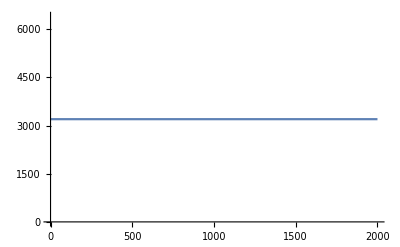
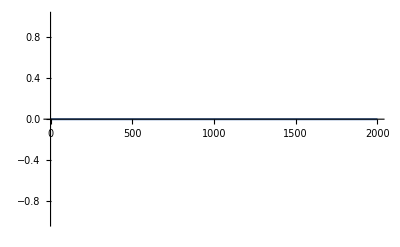
<|{2,1->2}→-Graphics-,{ex81,2->ex81}→-Graphics-,{1,en80->1}→-Graphics-,{1,1->2}→-Graphics-,{2,2->ex81}→-Graphics-,{en80,en80->1}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.